## Яковчик И.А.

## Lab_work_1: Списки. Строки и текст

## 1.1

### 1. Используя функцию Range создайте список {1,2,3,4}

```mathematica
Range[4](*Made list {1,2,3,4}*)
```

{1,2,3,4}

### 2. Создайте список из натуральных чисел от 1 до 100

```mathematica
Range[100](*Made a list reals numbers from 1 to 100*)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

### 3. Используя функции Range и Reverse, создайте список {4,3,2,1}

```mathematica
Reverse[Range[4]] (* Made a reverse list {4,3,2,1} *)
```

{4,3,2,1}

### 4. Создайте список из натуральных чисел от 1 до 50 в обратном порядке

```mathematica
Reverse[Range[50]](* Made a reverse list from 50 to 1 *)
```

{50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

### 5. Используя функции Range, Reverse и Join, создайте список {1,2,3,4,4,3,2,1}

```mathematica
Join[Range[4],Reverse[Range[4]]] (*made 2 join lists*)
```

{1,2,3,4,4,3,2,1}

### 6. Нарисовать график списка чисел, которые возрастают от 1 до 100, а затем убывают от 100 до 1

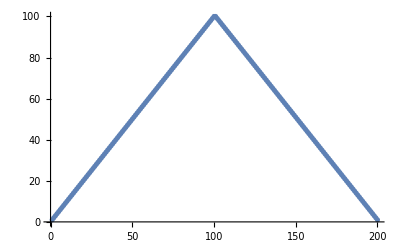

```mathematica
ListPlot[Join[Range[100],Reverse[Range[100]]]] (*made a chart of 2 lists*)
```

### 7. Используя функции Range и RandomInteger создайте список случайно генерированной длины, не превышающей число 10

```mathematica
Range[RandomInteger[10]](*made a list of random numbers*)
```

{1,2}

### 8. Найти простейшую форму для команды Reverse[Reverse[Range[10]]]

```mathematica
Range[10](*упростил команду *)
```

{1,2,3,4,5,6,7,8,9,10}

### 9. Найти простейшую форму для команды Join[{1,2},Join[{3,4},{5}]]

```mathematica
Join[{1,2},{3,4,5}](*упростил команду *)
```

{1,2,3,4,5}

### 10. Найти простейшую форму для команды Join[Range[10],Join[Range[10],Range[5]]]

```mathematica
Join[Range[10],Range[10],Range[5]](*проверил что выводит команда из задания *)
```

{1,2,3,4,5,6,7,8,9,10,1,2,3,4,5,6,7,8,9,10,1,2,3,4,5}

### 11. Найти простейшую форму для команды Reverse[Join[Range[20],Reverse[Range[20]]]]

```mathematica
Join[Range[20],Reverse[Range[20]]](*упростил команду *)
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,20,19,18,17,16,15,14,13,12,11,10,9,8,7,6,5,4,3,2,1}

## 1.2 Строки и текст (Strings and Text)

### 1. Присоедините две копии строки «Здравствуйте».

```mathematica
StringJoin["Здравствуйте","Здравствуйте"]
```

ЗдравствуйтеЗдравствуйте

### 2. Создайте единую строку всего английского алфавита заглавными буквами.

```mathematica
ToUpperCase[Alphabet[]](*создал строку с алфавитом заглавными буквами*)
```

{A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z}

### 3. Сгенерируйте строку английского алфавита в обратном порядке.

```mathematica
Reverse[Alphabet[]](*сгенерировал строку алфавита в обратном порядке*)
```

{z,y,x,w,v,u,t,s,r,q,p,o,n,m,l,k,j,i,h,g,f,e,d,c,b,a}

### 4. Объедините 100 копий строки «ABCD»

```mathematica
StringJoin[StringRepeat["ABCD",100]]
```

ABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCDABCD

### 5. Используйте StringTake, StringJoin и Alphabet, чтобы получить «abcdef»

```mathematica
StringTake[StringJoin[Alphabet[]],6](*выделил первые 6 букв алфавита*)
```

abcdef

### 6. Создайте столбец с числом элементов, равных длине строки «это о строках» и содержащих число букв (включая пробелы) равное номеру элемента.

```mathematica
Column[Table[StringTake["это о строках",n],{n,StringLength["это о строках"]}]](*с помощью отбора первых символов из строки вывел нужный столбец*)
```

э
эт
это
это 
это о
это о 
это о с
это о ст
это о стр
это о стро
это о строк
это о строка
это о строках

### 7. Создайте гистограмму длин слов в «Давным-давно, в далекой галактике, далеко».

```mathematica
StringLength[TextWords["Давным-давно, в далекой галактике, далеко"]]
```

{12,1,7,9,6}

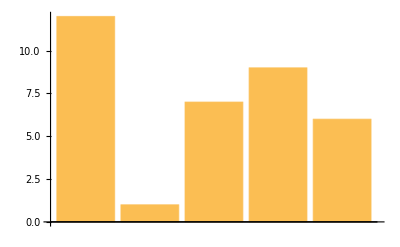

```mathematica
BarChart[StringLength[TextWords["Давным-давно, в далекой галактике, далеко"]]](*создал гистограмму*)
```

### 8. Найдите максимальную длину слова среди английских слов из WordList []

```mathematica
Max[StringLength[WordList[]]](*нашел длинну самого большого английского слова*)
```

23

### 9. Используйте Length, чтобы найти длину русского алфавита

```mathematica
Length[Alphabet["Russian"]](*нашел длинну русского алфавита*)
```

33

### 10. Создайте строку из заглавных букв греческого алфавита в обратном порядке.

```mathematica
StringJoin[ToUpperCase[Reverse[Alphabet["Greek"]]]]
```

ΩΨΧΦΥΤΣΡΠΟΞΝΜΛΚΙΘΗΖΕΔΓΒΑ

## 1.3 Чистые функции (Pure functions)

### 1. Используйте Range и чистую функцию для создания списка из квадратов первых 20 натуральных чисел.

```mathematica
#^2&/@Range[20](*возвёл в квадрат первые 20 натуральных чисел*)
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400}

### 2. Составьте список из результатов смешивания желтого, зеленого и синего цветов с красным цветом.

```mathematica
Blend[{#,Red},1/2]&/@{Yellow,Green,Blue}(*смешал 3 цвета с красным по очереди*)
```

{RGBColor[1, Rational[1, 2], 0],RGBColor[Rational[1, 2], Rational[1, 2], 0],RGBColor[Rational[1, 2], 0, Rational[1, 2]]}

### 3. Создайте список столбцов в рамках, содержащих прописные и строчные версии каждой буквы алфавита.

```mathematica
Framed[Column[{#,ToUpperCase[#]}]]&/@Alphabet[](*разделил буквы алфавита на прописные и строчные*)
```

{a
A,b
B,c
C,d
D,e
E,f
F,g
G,h
H,i
I,j
J,k
K,l
L,m
M,n
N,o
O,p
P,q
Q,r
R,s
S,t
T,u
U,v
V,w
W,x
X,y
Y,z
Z}

### 4. Составьте список букв алфавита в случайных цветах в рамках, имеющих случайные цвета фона.

```mathematica
(*каждая буква имеет свою рамку и цвет бэкграунда*)
```

```mathematica
Framed[Style[#,RandomColor[]],Background->RandomColor[]]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

### 5. Напишите в более простой форме команду (#^2+1&)/@Range[10].

```mathematica
Range[10]^2+1
```

{2,5,10,17,26,37,50,65,82,101}

## 1.4 Композиции функций и их программирование

### 1. Составьте список результатов использования функции Blur до 10 раз, начиная с растрированного размера 30 “X” (Используйте: Rasterize[Style]).

```mathematica
NestList[Blur,Rasterize[x,RasterSize->30],10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### 2. Начните с x, затем создайте список, использовав последовательно функцию Framed до 10 раз, используя каждый раз случайный цвет фона.

```mathematica
NestList[Framed[#,Background->RandomColor[]]&,x,10](*окрасил каждый слой вокруг Х в рандомный цвет*)
```

{x,x,x,x,x,x,x,x,x,x,x}

### 3. Начните с размера 50 для “A”, затем создайте список вложенного применения Framed и случайного вращения 5 раз.

```mathematica
NestList[Rotate[Framed[#],Pi*Random[]]&,Style["A",FontSize->50],5](*Повернул в рамке букву А на рандомное кол-во градусов*)
```

{A,A,A,A,A,A}

### 4. Создайте линейный график из 100 итераций логического итерационного отображения 4 #(1- #)&, начиная с 0.2.

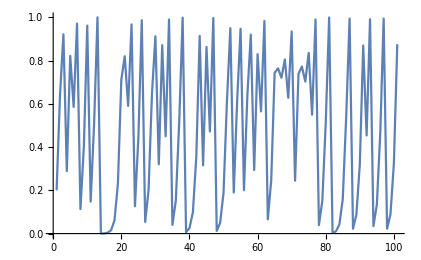

{0.2,0.64,0.9216,0.289014,0.821939,0.585421,0.970813,0.113339,0.401974,0.961563,0.147837,0.503924,0.999938,0.000246305,0.000984976,0.00393603,0.0156821,0.0617448,0.23173,0.712124,0.820014,0.590364,0.967337,0.126384,0.441645,0.986379,0.053742,0.203415,0.64815,0.912207,0.320342,0.870893,0.449755,0.989902,0.0399856,0.153547,0.519882,0.998419,0.00631451,0.0250985,0.0978744,0.35318,0.913776,0.315159,0.863335,0.47195,0.996853,0.0125495,0.0495681,0.188445,0.611733,0.950063,0.189772,0.615035,0.947067,0.200523,0.641254,0.920189,0.293764,0.829868,0.56475,0.98323,0.0659554,0.246421,0.742791,0.76421,0.720773,0.805037,0.62781,0.934659,0.244287,0.738444,0.772578,0.702804,0.835482,0.549808,0.990077,0.0393,0.151022,0.512857,0.999339,0.00264312,0.0105445,0.0417334,0.159967,0.53751,0.994372,0.0223857,0.0875383,0.319501,0.869681,0.453344,0.991293,0.0345245,0.13333,0.462213,0.994289,0.0227147,0.088795,0.323642,0.875591}

```mathematica
ListLinePlot[NestList[4 #(1-#)&,0.2,100]]

NestList[4 #(1-#)&,0.2,100]
```

### 5. Найдите числовое значение результата из 30 итераций применения функции 1+1/#&, начиная с 1

```mathematica
Nest[1+1/#&,1,30]
```

2178309/1346269

### 6. Создайте список из первых 10 степеней 3 (начиная с 0) путем вложенного умножения.

```mathematica
NestList[3*#&,1,10](*вывел первые 10 степеней тройки*)
```

{1,3,9,27,81,243,729,2187,6561,19683,59049}

### 7. Составьте список результатов действия вложенной функции (метод Ньютона) (# + 2 / #) / 2 до 5 раз, начиная с 1.0, а затем вычтите 2 из всех результатов.

```mathematica
NestList[(#+2/#)/2-2&,1.0,5]
```

{1.,-0.5,-4.25,-4.36029,-4.40949,-4.43153}

### 8. Создайте список из 5 степеней числа 2, т. е. 2 ^ 2 ^ 2 ... ^ 2 n раз, причем n меняется от 0 до 4.

```mathematica
Table[NestList[#^2&,2,4],1]//Flatten
```

{2,4,16,256,65536}

## 1.5 Определение функций пользователя

### 1. Определите функцию f, которая вычисляет квадрат ее аргумента.

```mathematica
f[x_]:= x^2(*определил функцию которая вычисляет квадрат числа*)
```

```mathematica
f[16]
```

256

### 2. Определите функцию poly, которая имеет целочисленное значение аргумента и создает изображение оранжевого правильного многоугольника с числом сторон, равным значению этого аргумента.

```mathematica
poly[x_]:= Graphics[Style[RegularPolygon[x],Orange]](*определил фукнцию рисующую правильный многоугольник оранжевого цвета*)
```

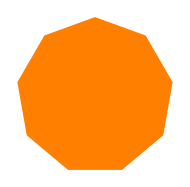

```mathematica
poly[9]
```

### 3. Определите функцию f, которая берет список из двух элементов и помещает их в обратном порядке.

```mathematica
f[x_] := Reverse[x] (*определил фукнцию которая обращает список*)
f[{100,50}]
```

{50,100}

### 4. Определите функцию f, которая имеет два аргумента и дает результат в виде дроби, где числитель равен произведению этих элементов, а знаменатель - их сумме.

```mathematica
f[x_,y_] := (x*y)/(x+y) (*определил функцию вычисляющую дробь*)
f[5,4]
```

20/9

### 5. Определите функцию f, которая имеет два аргумента и дает результат в виде списка трех элементов, которые соответственно равны сумме, разности и частному этих аргументов.

```mathematica
f[x_,y_]:={x+y,x-y,x/y} (*определил функцию которая принимает 2 аргумента и проивзодит вычисления с ними*)
f[10,5]
```

{15,5,2}

### 6. Определите функцию evenodd, которая зависит от одного целочисленного аргумента и имеет значение Black, если ее аргумент четный, значение - White в противном случае, значение Red - если аргумент равен нулю

```mathematica
evenodd[x_]:= If[EvenQ[x],Black,White]; evenodd[0] = Red;(*определил функцию которая окрашивает в разные цвета в зависимости от аргумента*)
evenodd[15]
```

GrayLevel[1]

### 7. Определите функцию Fibonacci f с f [0]=1 и f [1]=1, а f [n] для натурального числа n является суммой f [n-1] и f [n-2].

```mathematica
f[0]:=0  (*определил функцию фибоначи для n*)
f[1]:=1
f[n_] := f[n-1]+f[n-2]
f[10]
```

55

```mathematica
Fibonacci[10]
```

55